3-D Harmonic Oscillator

H=-1/2∇^2 +1/2 r^2=-1/2∇^2 +1/2(x^2+y^2+z^2)=H_x+H_y+H_z

H_x only operates on x, H_yon y, H_zon z so ψ_(n_x,n_y,n_z)=u_x(x)u_y(y)u_z(z)
this is 3 1-D SHOs so the energies are

ϵ_(n_x,n_y,n_z)=(n_x+1/2)+(n_y+1/2)+(n_z+1/2)=n_x+n_y+n_z+3/2

In spherical coordinates ψ_(n,l,m)=P_(l,n)Y_lm

H_l=-1/2 ⅆ_r^2+((l(l+1))/(2 r^2)+1/2 r^2)

Find gnd state solution, guess P_l0=r^(l+1)ⅇ^(-r^2/2) with energy ϵ_(l,0)

```mathematica
With[{Pl0=r^(l+1)ⅇ^(-r^2/2)},
-1/2 D[Pl0, r,r]+((l(l+1))/(2 r^2)+1/2 r^2)Pl0==Subscript[ϵ, l,0] Pl0//Simplify]
```

ⅇ^(-r^2/2) r^(1+l) (3+2 l-2 ϵ_(l,0))==0

True if ϵ_(l,0)=l+3/2.  

See if this obeys supersymmetry:

```mathematica
W[l_]=With[{Pl0=r^(l+1)ⅇ^(-r^2/2)},-D[Pl0, r]/Pl0//Simplify]
```

(-1-l+r^2)/r

```mathematica
V[l_]=(l(l+1))/(2 r^2)+1/2 r^2;
```

```mathematica
V[l+1]-V[l]//Simplify
```

(1+l)/r^2

```mathematica
D[W[l], r]//Simplify
```

(1+l+r^2)/r^2

Since these are not equal, we need to add a l-dependent constant to V_l to make supersymmetry work.  So let V_l^ss=V_l+l and ϵ_(l,k)^ss=ϵ_(o,k)+l:

```mathematica
Vs[l_]=V[l]+l;
```

```mathematica
Vs[l+1]-Vs[l]==D[W[l], r]//Simplify
```

True

So ϵ_l0^ss=2l+3/2→ ϵ_(l,k)^ss=2(l+k)+3/2→ ϵ_(l,k)=ϵ_(l,k)^ss-l=2k+l+3/2

```mathematica
sho3=Table[{l,2k+l+3/2},{l,0,4},{k,0,4}]~Flatten~1
```

{{0,3/2},{0,7/2},{0,11/2},{0,15/2},{0,19/2},{1,5/2},{1,9/2},{1,13/2},{1,17/2},{1,21/2},{2,7/2},{2,11/2},{2,15/2},{2,19/2},{2,23/2},{3,9/2},{3,13/2},{3,17/2},{3,21/2},{3,25/2},{4,11/2},{4,15/2},{4,19/2},{4,23/2},{4,27/2}}

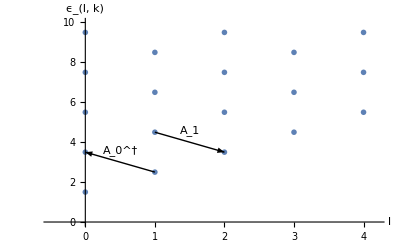

```mathematica
ListPlot[sho3,PlotMarkers->Graphics@Line[{{0,0},{.2,0}}],PlotRange->{{-.5,4.2},{0,10}},AxesLabel->{"l","ϵ_(l, k)"},Epilog->{Arrow[{{1,5/2},{0,7/2}}],Arrow[{{1,9/2},{2,7/2}}],Inset["A_0^†",{.5,3.6}],Inset["A_1",{1.5,4.6}]}]
```